## Lab 9- GWEN GORMAN

Use the functions PlotRightEndpointApproximation and RightEndpointApproximation to make animation that shows the estimated area enclosed by y=0,y=3+2cos x,x=π/2, and x=π, using various number of subintervals. Tips: You would have to experiment with arguments passed to PlotRightEndpointApproximation so that the animation not only works but also looks good.

```mathematica
RightEndpointApproximation[func_,a_,b_,n_]:=Module[
{f,h},
f[X_]=func/.x->X;
h=(b-a)/n//N;
Sum[f[a+i h],{i,1,n}]*h
];
```

```mathematica
RightEndpointApproximation[3+2Cos[x],Pi/2,Pi,10]
```

2.55942

```mathematica
Manipulate[
Module[{f,a,b,toString,PlotRightEndpointApproximation,RightEndpointApproximation},
f[x_]:=3+2Cos[x];
a=Pi/2;b=π;
toString[x_]:=ToString[If[Abs[x]<10^-5,0,x]];

PlotRightEndpointApproximation[func_,a_,b_,n_,xMin_,xMax_,abYPos_,fYPos_,plotRange_,ticks_, axesLabel_, showExtraMsg_]:=Module[
{f,h=(b-a)/n},
f[X_]=func/.x->X;
Show[{ 
Plot[f[x],{x,xMin,xMax},plotRange,ticks,axesLabel,ImageSize->320],
Plot[{f[x],0},{x,a,b},Filling->{1->{2}}],
Graphics[{Text[a,{a,abYPos}]}],
Graphics[{Text[b,{b,abYPos}]}],
Graphics[{Text[f[x],{(xMin+xMax)/2,fYPos}]}],
{showExtraMsg},
Table[Graphics[Line[{{a+i*h,0},{a+i*h,Max[{f[a+i h],f[a+(i+1)*h]}]}}]],{i,0,n-1}],
Graphics[Line[{{b,0},{b,f[b]}}]],
Table[Graphics[Line[{{a+(i-1)*h,f[a+i*h]},{a+i*h,f[a+i*h]}}]],{i,1,n}]
}]
];
RightEndpointApproximation[func_,a_,b_,n_]:=Module[
{f,h},
f[X_]=func/.x->X;
h=(b-a)/n//N;
Sum[f[a+i h],{i,1,n}]*h
];
PlotRightEndpointApproximation[f[x],a,b,n,a-0.1,b+0.1,-0.1,1.2,PlotRange->{-0.5,1.5},Ticks->False,AxesLabel->{x,y},Graphics[{Text[StringJoin["n = ",ToString[n],"       Area ≈ ",toString[RightEndpointApproximation[f[x],a,b,n]]],{(a+b)/2,-0.2}]}]]],
{{n,15},1,200,1}]
```

Construct a table that shows the three basic numerical approximations, left-endpoint, right-endpoint, and midpoint approximations, for the area bounded by x=π/2,x=π,y=3+2cos x, and y=0, corresponding to n=2,4,10,20,40,80.

```mathematica
Module[{f,a,b,h},
f[x_]:=3+2Cos[x];
a=Pi/2;b=Pi;
h:=N[(b-a)/n]; 
Join[
{{"n","Left-Endpoint", "Right-Endpoint","Midpoint"}},
Table[{
n,
Sum[f[a+i h],{i,0,n-1}]*h,
Sum[f[a+i h],{i,1,n}]*h,
Sum[f[a+(i-1/2) h],{i,1,n}]*h,
},{n,{2,4,10,20,40,80}}] 
]//TableForm
]
```

n | Left-Endpoint | Right-Endpoint | Midpoint | 
2 | 3.60167 | 2.03087 | 2.66004 | Null
4 | 3.13086 | 2.34546 | 2.69948 | Null
10 | 2.87358 | 2.55942 | 2.71033 | Null
20 | 2.79196 | 2.63488 | 2.71187 | Null
40 | 2.75192 | 2.67338 | 2.71226 | Null
80 | 2.73209 | 2.69282 | 2.71236 | Null

Use 10 subintervals and midpoint approximation to estimate the area under the curve of y=x ⅇ^x for 0≤x≤2.

```mathematica
MidpointApproximation[func_,a_,b_,n_]:=Module[
{f,h},
f[X_]=func/.x->X;
h=(b-a)/n//N;
Sum[f[a+(i-1/2) h],{i,1,n}]*h
];
```

```mathematica
MidpointApproximation[x ⅇ^x,0,2,10]
```

8.35384

For each function, using the trapezoidal approximation to compute the exact area under its curve and above the x-axis on the specified interval.

f(x)=x sin x, [0,π]

```mathematica
TrapezoidalApproximation[func_,a_,b_,n_]:=Module[
{f,h},
f[X_]=func/.x->X;
h=(b-a)/n//N;
Sum[f[a+(i-1) h]+f[a+i h],{i,1,n}]*h/2
];
```

```mathematica
TrapezoidalApproximation[x*Sin[x],0,Pi,10000]
```

3.14159

f(x)=x^2 sin x,[0,π]

```mathematica
TrapezoidalApproximation[func_,a_,b_,n_]:=Module[
{f,h},
f[X_]=func/.x->X;
h=(b-a)/n//N;
Sum[f[a+(i-1) h]+f[a+i h],{i,1,n}]*h/2
];
TrapezoidalApproximation[x^2*Sin[x],0,Pi,10000]
```

5.8696

f(x)=ⅇ^x,[0,1]

```mathematica
TrapezoidalApproximation[func_,a_,b_,n_]:=Module[
{f,h},
f[X_]=func/.x->X;
h=(b-a)/n//N;
Sum[f[a+(i-1) h]+f[a+i h],{i,1,n}]*h/2
];
```

```mathematica
TrapezoidalApproximation[ⅇ^x,0,1,10000]
```

1.71828

Applying the fundamental theorem of integral calculus, redo Question 4.

```mathematica
Clear["Global"]
```

```mathematica
F[x_]=Integrate[x*Sin[x],x]
```

-x Cos[x]+Sin[x]

```mathematica
F[Pi]-F[0]
```

π

```mathematica
F[x_]=Integrate[x^2*Sin[x],x]
```

-(-2+x^2) Cos[x]+2 x Sin[x]

```mathematica
F[Pi]-F[0]
```

-4+π^2

```mathematica
N[-4+π^2]
```

5.8696

```mathematica
F[x_]=Integrate[ⅇ^x,x]
```

ⅇ^x

```mathematica
F[1]-F[0]
```

-1+ⅇ

```mathematica
N[-1+ⅇ]
```

1.71828

Using Mathematica built-in function Integrate, redo Question 4.

```mathematica
Integrate[x*Sin[x],{x,0,Pi}]
```

π

```mathematica
Integrate[x^2*Sin[x],{x,0,Pi}]
```

-4+π^2

```mathematica
N[-4+π^2]
```

5.8696

```mathematica
Integrate[ⅇ^x,{x,0,1}]
```

-1+ⅇ

```mathematica
N[-1+ⅇ]
```

1.71828

Construct a table that shows the four basic numerical approximations, i.e., the left-endpoint, right-endpoint, midpoint, and trapezoidal approximations, as well as Simpson’s 1/3 and 3/8 methods, for the area bounded by x=0,x=π,y=0, and y=sin x, corresponding to n=1,2,3,4, 5,6,12,24,48, 96,192,384,768, 1536,3072.

```mathematica
SixApproximations[func_,a_,b_,n_]:=Module[{f,h=(b-a)/n,d=7},
f[X_]=func/.x->X;
{n,
N[Sum[f[a+i h],{i,0,n-1}]*h,d],
N[Sum[f[a+i h],{i,1,n}]*h,d],
N[Sum[f[a+(i-1/2) h],{i,1,n}]*h,d],
N[Sum[f[a+(i-1) h]+f[a+i h],{i,1,n}]*h/2,d],
If[Mod[n,2]==0,(* divisible by 2 *)
N[1/3*h*Sum[f[a+i h]+4f[a+(i+1) h]+f[a+(i+2)h],{i,0,n-2,2}],d],
"N/A"],
If[Mod[n,3]==0,(* divisible by 3 *)
N[3/8*h*Sum[f[a+i h]+3f[a+(i+1) h]+3f[a+(i+2)h]+f[a+(i+3)h],{i,0,n-3,3}] ,d],
"N/A"]
}
]
```

```mathematica
Module[{f,a=0,b=Pi},
f[x_]:=Sin[x];
TableForm[
Join[
{{"n","Left-End", "Right-End","Midpoint","Trapezoid","Simpson 1/3", "Simpson 3/8"}},
Table[SixApproximations[f[x],a,b,n],{n,{1,2,3,4,5,6,12,24,48,96,192,384,768,1536,3072}}]
],TableAlignments->Right]
]
```

n | Left-End | Right-End | Midpoint | Trapezoid | Simpson 1/3 | Simpson 3/8
1 | 0 | 0 | 3.141593 | 0 | N/A | N/A
2 | 1.570796 | 1.570796 | 2.221441 | 1.570796 | 2.094395 | N/A
3 | 1.813799 | 1.813799 | 2.094395 | 1.813799 | N/A | 2.040524
4 | 1.896119 | 1.896119 | 2.052344 | 1.896119 | 2.00456 | N/A
5 | 1.933766 | 1.933766 | 2.033281 | 1.933766 | N/A | N/A
6 | 1.954097 | 1.954097 | 2.02303 | 1.954097 | 2.000863 | 2.00201
12 | 1.988564 | 1.988564 | 2.005723 | 1.988564 | 2.000053 | 2.000119
24 | 1.997143 | 1.997143 | 2.001429 | 1.997143 | 2.000003 | 2.000007
48 | 1.999286 | 1.999286 | 2.000357 | 1.999286 | 2. | 2.
96 | 1.999822 | 1.999822 | 2.000089 | 1.999822 | 2. | 2.
192 | 1.999955 | 1.999955 | 2.000022 | 1.999955 | 2. | 2.
384 | 1.999989 | 1.999989 | 2.000006 | 1.999989 | 2. | 2.
768 | 1.999997 | 1.999997 | 2.000001 | 1.999997 | 2. | 2.
1536 | 1.999999 | 1.999999 | 2. | 1.999999 | 2. | 2.
3072 | 2. | 2. | 2. | 2. | 2. | 2.

Repeat Question 7 with y=sin x replaced by y=cos x. Plot the graph of cos x and explain why the net area is zero. Since the midpoint and trapezoidal approximations work here as fast as Simpson’s 1/3 and 3/8 methods do, can we draw any general conclusion?

```mathematica
SixApproximations[func_,a_,b_,n_]:=Module[{f,h=(b-a)/n,d=7},
f[X_]=func/.x->X;
{n,
N[Sum[f[a+i h],{i,0,n-1}]*h,d],
N[Sum[f[a+i h],{i,1,n}]*h,d],
N[Sum[f[a+(i-1/2) h],{i,1,n}]*h,d],
N[Sum[f[a+(i-1) h]+f[a+i h],{i,1,n}]*h/2,d],
If[Mod[n,2]==0,(* divisible by 2 *)
N[1/3*h*Sum[f[a+i h]+4f[a+(i+1) h]+f[a+(i+2)h],{i,0,n-2,2}],d],
"N/A"],
If[Mod[n,3]==0,(* divisible by 3 *)
N[3/8*h*Sum[f[a+i h]+3f[a+(i+1) h]+3f[a+(i+2)h]+f[a+(i+3)h],{i,0,n-3,3}] ,d],
"N/A"]
}
]
```

```mathematica
Module[{f,a=0,b=Pi},
f[x_]:=Cos[x];
TableForm[
Join[
{{"n","Left-End", "Right-End","Midpoint","Trapezoid","Simpson 1/3", "Simpson 3/8"}},
Table[SixApproximations[f[x],a,b,n],{n,{1,2,3,4,5,6,12,24,48,96,192,384,768,1536,3072}}]
],TableAlignments->Right]
]
```

n | Left-End | Right-End | Midpoint | Trapezoid | Simpson 1/3 | Simpson 3/8
1 | 3.141593 | -3.141593 | 0 | 0 | N/A | N/A
2 | 1.570796 | -1.570796 | 0 | 0 | 0 | N/A
3 | 1.047198 | -1.047198 | 0 | 0 | N/A | 0
4 | 0.7853982 | -0.7853982 | 0 | 0 | 0 | N/A
5 | 0.6283185 | -0.6283185 | 0 | 0. | N/A | N/A
6 | 0.5235988 | -0.5235988 | 0 | 0 | 0 | 0
12 | 0.2617994 | -0.2617994 | 0 | 0 | 0 | 0
24 | 0.1308997 | -0.1308997 | 0 | 0 | 0 | 0
48 | 0.06544985 | -0.06544985 | 0 | 0 | 0 | 0
96 | 0.03272492 | -0.03272492 | 0 | 0 | 0 | 0
192 | 0.01636246 | -0.01636246 | 0 | 0 | 0 | 0
384 | 0.008181231 | -0.008181231 | 0 | 0 | 0 | 0
768 | 0.004090615 | -0.004090615 | 0 | 0 | 0 | 0
1536 | 0.002045308 | -0.002045308 | 0 | 0 | 0 | 0
3072 | 0.001022654 | -0.001022654 | 0 | 0 | 0 | 0

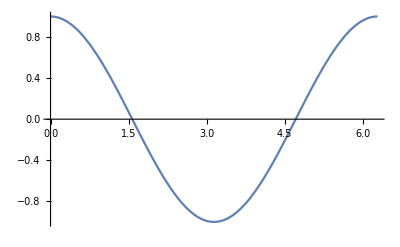

```mathematica
Plot[Cos[x],{x,0,2Pi},PlotRange->Automatic]
```

The area above the x-axis is the same as the area below the x-axis. However, the area below the x-axis is negative and when added to the area above the x-axis, the net area is zero. Since the midpoint and trapezoidal approximations work as fast at the Simpsons 1/3 and 3/8’s method, we can conclude that this area is relatively simple to calculate.

Finding the area of the shaded region, where a and b are the x-coordinates of the points where the two curves intersect each other.

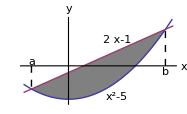

```mathematica
Integrate[(2x-1)-(x^2-5),{x,-1.236,3.236}]//N
```

14.9071

The area of the shaded region is 14.9071 units.

Finding the area of the shaded region, where a is the x-coordinate of the left intersection of the two curves.

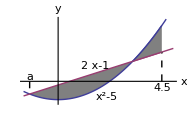

```mathematica
NSolve[2x-1==x^2-5&&-1.236≤x≤4.5,x]
```

{{x→3.23607}}

```mathematica
x0=x/.%[[1]]
```

3.23607

```mathematica
Integrate[(2x-1)-(x^2-5),{x,-1.236,x0}]+Integrate[(x^2-5)-(2x-1),{x,x0,4.5}]
```

19.1523

The area of the shaded region is 19.1523 units.

With the help of Mathematica, evaluate each improper integral, and determine its convergence.

∫_1^∞ 1/x ⅆx

```mathematica
Assuming[t>1,Integrate[1/x,{x,1,t}]]
Limit[%,t->∞]
```

Log[t]

∞

The improper integral diverges.

∫_1^∞ 1/x^2 ⅆx

```mathematica
Assuming[t>1,Integrate[1/x^2,{x,1,t}]]
Limit[%,t->∞]
```

(-1+t)/t

1

The improper integral converges at 1.

∫_(-∞)^∞ e^(-x^2)ⅆx

```mathematica
Integrate[ⅇ^(-x^2),{x,t,0}]
Limit[%,t->-∞]
```

-1/2 √π Erf[t]

(√π)/2

```mathematica
Integrate[ⅇ^(-x^2),{x,t,0}]
Limit[%,t->∞]
```

-1/2 √π Erf[t]

-(√π)/2

Computing the two boundaries we see that (√π)/2-((-√π)/2)=√π. So, the improper integral converges at √π.

∫_0^2 1/(x^2-4)ⅆx

```mathematica
Assuming[0<t<2,Integrate[1/(x^2-4),{x,0,t}]]
```

1/4 Log[(2-t)/(2+t)]

```mathematica
Limit[%,t->0,Direction->2]
```

0

The improper integral converges at 0.